```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"];
```

```mathematica
(* Тест 1*)
solve := Sin[0.5 t];
data1=Import["fnauto1-rungekutta2auto-0","Table"];
(*data2=Import["fnauto1-rungekutta4auto-0","Table"]*)
data3=Import["fnauto1-rungekutta2-0","Table"];
data4=Import["fnauto1-eulersimple-0","Table"];

(* Модуль для отрисоввки графиков *)
TEST[solve_, data_]  := Module[{plotsolve1, plot1data1,plot2data1, ploterror1,plot1, plot2, plot3},
plotsolve1= Plot[solve,{t,0,10},PlotStyle->{Red,Dashed}];

plot1data1= ListPlot[Table[{data[[i]][[1]],data[[i]][[2]]},{i,1,Length[data]}],Joined->True];


ploterror1 = ListPlot[Table[{data[[i]][[1]], Abs[(solve/.t->data[[i]][[1]])-data[[i]][[2]]]}, {i,1,Length[data]}], Joined->True,AxesLabel->{"t", "ERROR"}];
plot1 = Show[plot1data1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],plotsolve1,AxesLabel->{"t", "u"},AxesStyle->Arrowheads[0.03], PlotLabel -> "1) Сравнение численного решения с аналитическим",LabelStyle -> Below,ImageSize->400];
plot2 = Show[ploterror1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],AxesLabel->{"t", "Error"},AxesStyle->Arrowheads[0.03], PlotLabel-> "2) График ошибки",ImageSize->400];
plot3 = Show[ListPlot[Table[{data[[i]][[1]], Abs[data[[i]][[1]]-data[[i+1]][[1]]]}, {i,1,Length[data]-1}], Joined->True,AxesLabel->{"t", "h"},   PlotLabel-> "3) Изменение шага по времени ",ImageSize->400]];

Show[GraphicsColumn[{plot1, plot2, plot3}, ImageSize->500,Spacings->{0,0}], PlotLabel->"Иллюстрация работы выбора шага", LabelStyle->"Subsection"]

];
```

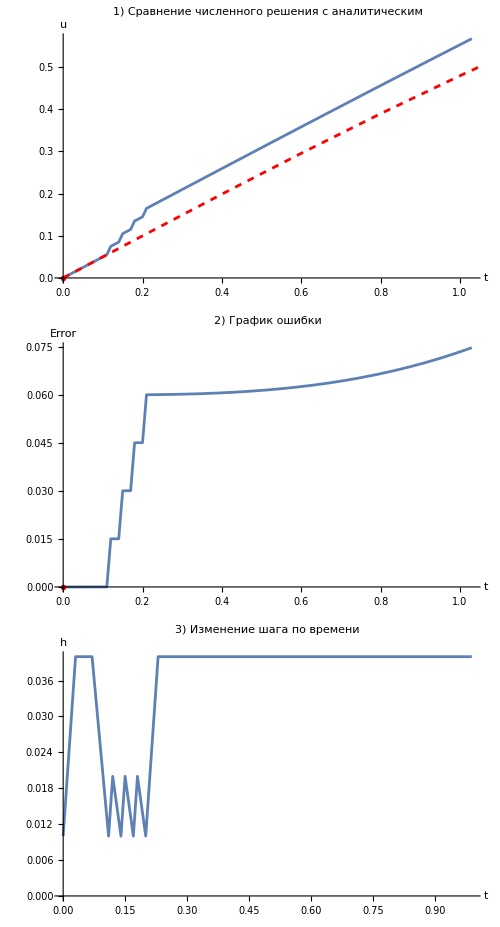

```mathematica
TEST[solve, data1]
```